```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
L[x_,a_,b_,c_,h_]:=a x^2+b x^4+c x^6+h x
```

```mathematica
xmin1[a_,b_,c_,h_]=x/.Solve[(D[L[xs,a,b,c,h],xs]/.xs->x)==0,{x}][[1]]//Quiet;
xmin2[a_,b_,c_,h_]=x/.Solve[(D[L[xs,a,b,c,h],xs]/.xs->x)==0,{x}][[2]]//Quiet;
xmin3[a_,b_,c_,h_]=x/.Solve[(D[L[xs,a,b,c,h],xs]/.xs->x)==0,{x}][[3]]//Quiet;
xmin4[a_,b_,c_,h_]=x/.Solve[(D[L[xs,a,b,c,h],xs]/.xs->x)==0,{x}][[4]]//Quiet;
xmin5[a_,b_,c_,h_]=x/.Solve[(D[L[xs,a,b,c,h],xs]/.xs->x)==0,{x}][[5]]//Quiet;
xmin6[a_,b_,c_,h_]=x/.Solve[(D[L[xs,a,b,c,h],xs]/.xs->x)==0,{x}][[6]]//Quiet;
```

```mathematica
xmin3[-2,0.7,1,0]//N
```

0.784761

### 2nd order transition

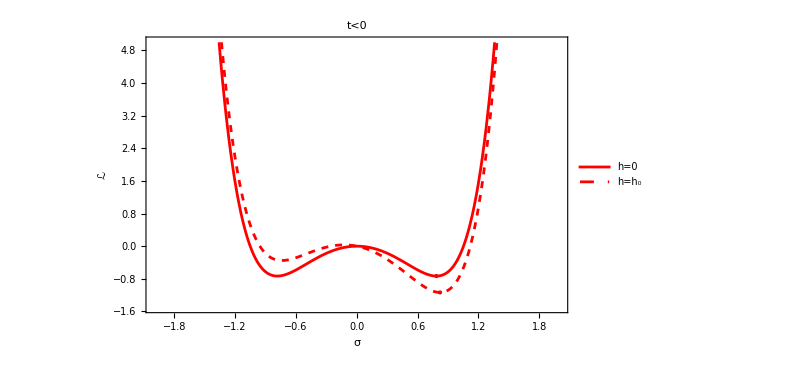

```mathematica
landau1=Show[{Plot[{L[x,-2,0.7,1,0],L[x,-2,0.7,1,-0.5]},{x,-2,2},PlotRange->{-1.5,5},PlotStyle->{Directive[Red,AbsoluteThickness[2]],Directive[Red,Dashed,AbsoluteThickness[2]]},Frame->True,AxesOrigin->{0,0},FrameLabel->{"σ","ℒ"},LabelStyle->{FontSize->16},PlotLabel->Style["t<0",FontSize->20],ImageSize->{600,400},PlotLegends->Placed[
LineLegend[
{Text[Style["h=0",FontSize->13]],
Text[Style["h=h_0",FontSize->13]]}],{Right,Center}]],ListPlot[{{xmin3[-2,0.7,1,0],L[xmin3[-2,0.7,1,0],-2,0.7,1,0]},{xmin3[-2,0.7,1,-0.5],L[xmin3[-2,0.7,1,-0.5],-2,0.7,1,-0.5]}},PlotStyle->{Directive[PointSize[Large],Red]}]}]
```

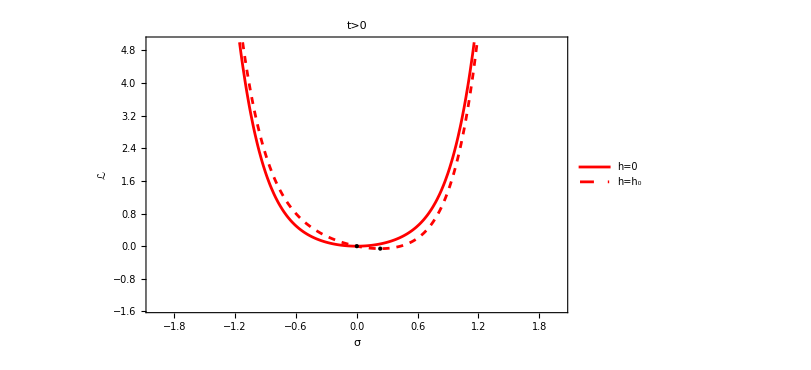

```mathematica
landau2=Show[{Plot[{L[x,1,0.7,1,0],L[x,1,0.7,1,-0.5]},{x,-2,2},PlotRange->{-1.5,5},PlotStyle->{Directive[Red,AbsoluteThickness[2]],Directive[Red,Dashed,AbsoluteThickness[2]]},Frame->True,AxesOrigin->{0,0},FrameLabel->{"σ","ℒ"},LabelStyle->{FontSize->16},PlotLabel->Style["t>0",FontSize->20],ImageSize->{600,400},PlotLegends->Placed[
LineLegend[
{Text[Style["h=0",FontSize->13]],
Text[Style["h=h_0",FontSize->13]]}],{Right,Center}]],ListPlot[{{xmin1[1,0.7,1,0],L[xmin1[1,0.7,1,0],1,0.7,1,0]},{xmin1[1,0.7,1,-0.5],L[xmin1[1,0.7,1,-0.5],1,0.7,1,-0.5]}},PlotStyle->{Directive[PointSize[Large],Black]}]}]
```

```mathematica
Export["landau_energy_2nd_ts0.pdf",landau1,"PDF"]
Export["landau_energy_2nd_tg0.pdf",landau2,"PDF"]
```

landau_energy_2nd_ts0.pdf

landau_energy_2nd_tg0.pdf

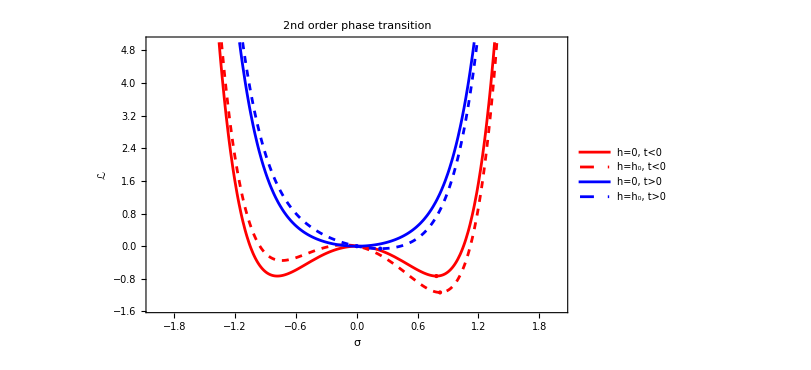

```mathematica
(*All together*)
landau2nd=Show[{Plot[{L[x,-2,0.7,1,0],L[x,-2,0.7,1,-0.5],L[x,1,0.7,1,0],L[x,1,0.7,1,-0.5]},{x,-2,2},PlotRange->{-1.5,5},PlotStyle->{Directive[Red,AbsoluteThickness[2]],Directive[Red,Dashed,AbsoluteThickness[2]],Directive[Blue,AbsoluteThickness[2]],Directive[Blue,Dashed,AbsoluteThickness[2]]},Frame->True,AxesOrigin->{0,0},FrameLabel->{"σ","ℒ"},LabelStyle->{FontSize->16},PlotLabel->Style["2nd order phase transition",FontSize->20],ImageSize->{600,400},PlotLegends->Placed[
LineLegend[
{Text[Style["h=0, t<0",FontSize->13]],
Text[Style["h=h_0, t<0",FontSize->13]],Text[Style["h=0, t>0",FontSize->13]],Text[Style["h=h_0, t>0",FontSize->13]]}],{Right,Center}]],ListPlot[{{xmin3[-2,0.7,1,0],L[xmin3[-2,0.7,1,0],-2,0.7,1,0]},{xmin3[-2,0.7,1,-0.5],L[xmin3[-2,0.7,1,-0.5],-2,0.7,1,-0.5]}},PlotStyle->{Directive[PointSize[Large],Red]}],
ListPlot[{{xmin1[1,0.7,1,0],L[xmin1[1,0.7,1,0],1,0.7,1,0]},{xmin1[1,0.7,1,-0.5],L[xmin1[1,0.7,1,-0.5],1,0.7,1,-0.5]}},PlotStyle->{Directive[PointSize[Large],Blue]}]}]
```

```mathematica
Export["landau_energy_2nd.pdf",landau2nd,"PDF"]
```

landau_energy_2nd.pdf

### 1st order transition

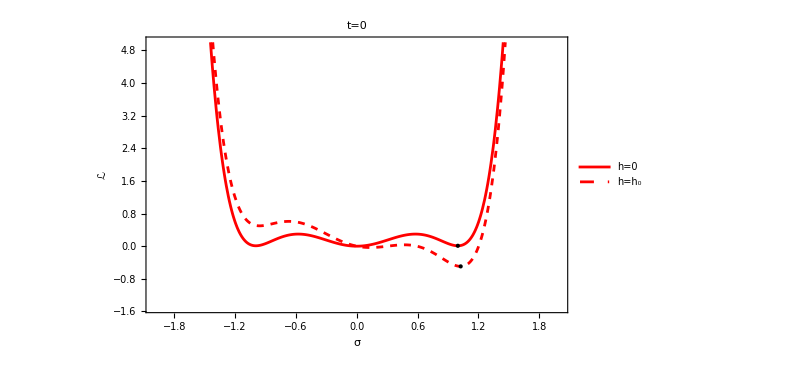

```mathematica
landau3=Show[{Plot[{L[x,2,-4,2.01,0],L[x,2,-4,2.01,-0.5]},{x,-2,2},PlotRange->{-1.5,5},PlotStyle->{Directive[Red,AbsoluteThickness[2]],Directive[Red,Dashed,AbsoluteThickness[2]]},Frame->True,AxesOrigin->{0,0},FrameLabel->{"σ","ℒ"},LabelStyle->{FontSize->16},PlotLabel->Style["t=0",FontSize->20],ImageSize->{600,400},PlotLegends->Placed[
LineLegend[
{Text[Style["h=0",FontSize->13]],
Text[Style["h=h_0",FontSize->13]]}],{Right,Center}]],ListPlot[{{xmin5[2,-4,2.01,0],L[xmin5[2,-4,2.01,0],2,-4,2.01,0]},{xmin5[2,-4,2.01,-0.5],L[xmin5[2,-4,2.01,-0.5],2,-4,2.01,-0.5]}},PlotStyle->{Directive[PointSize[Large],Black]}]}]
```

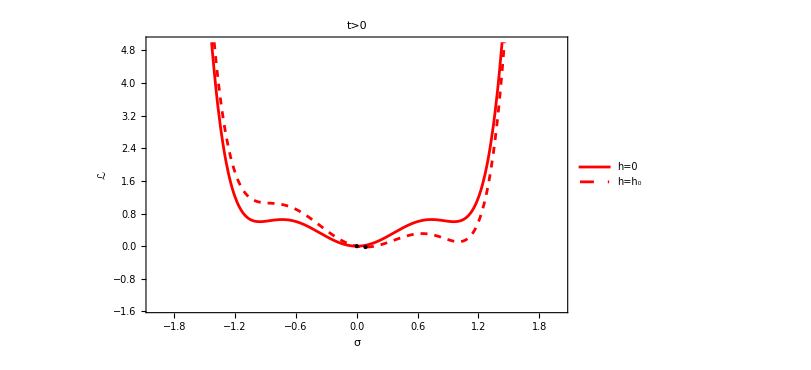

```mathematica
landau4=Show[{Plot[{L[x,3,-4.4,2.01,0],L[x,3,-4.4,2.01,-0.5]},{x,-2,2},PlotRange->{-1.5,5},PlotStyle->{Directive[Red,AbsoluteThickness[2]],Directive[Red,Dashed,AbsoluteThickness[2]]},Frame->True,AxesOrigin->{0,0},FrameLabel->{"σ","ℒ"},LabelStyle->{FontSize->16},PlotLabel->Style["t>0",FontSize->20],ImageSize->{600,400},PlotLegends->Placed[
LineLegend[
{Text[Style["h=0",FontSize->13]],
Text[Style["h=h_0",FontSize->13]]}],{Right,Center}]],ListPlot[{{xmin3[3,-4.4,2.01,0],L[xmin3[3,-4.4,2.01,0],3,-4.4,2.01,0]},{xmin1[3,-4.4,2.01,-0.5],L[xmin1[3,-4.4,2.01,-0.5],3,-4.4,2.01,-0.5]}},PlotStyle->{Directive[PointSize[Large],Black]}]}]
```

```mathematica
Export["landau_energy_1st_te0.pdf",landau3,"PDF"]
Export["landau_energy_1st_tg0.pdf",landau4,"PDF"]
```

landau_energy_1st_te0.pdf

landau_energy_1st_tg0.pdf

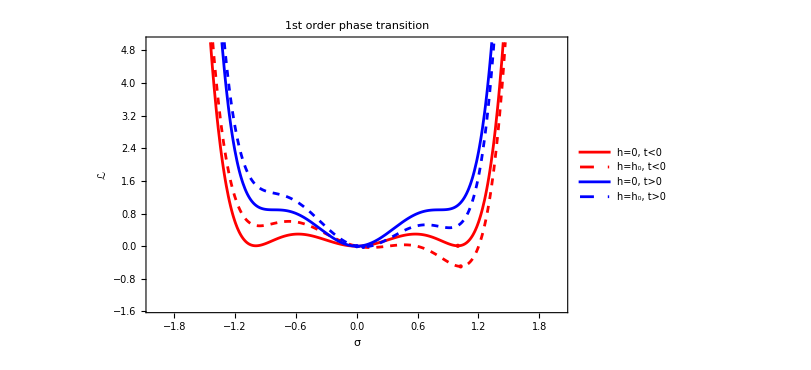

```mathematica
(*All together*)
landau1st=Show[{Plot[{L[x,2,-4,2.01,0],L[x,2,-4,2.01,-0.5],L[x,4,-6,3.01,0],L[x,4,-6,3.01,-0.5]+0},{x,-2,2},PlotRange->{-1.5,5},PlotStyle->{Directive[Red,AbsoluteThickness[2]],Directive[Red,Dashed,AbsoluteThickness[2]],Directive[Blue,AbsoluteThickness[2]],Directive[Blue,Dashed,AbsoluteThickness[2]]},Frame->True,AxesOrigin->{0,0},FrameLabel->{"σ","ℒ"},LabelStyle->{FontSize->16},PlotLabel->Style["1st order phase transition",FontSize->20],ImageSize->{600,400},PlotLegends->Placed[
LineLegend[
{Text[Style["h=0, t<0",FontSize->13]],
Text[Style["h=h_0, t<0",FontSize->13]],Text[Style["h=0, t>0",FontSize->13]],Text[Style["h=h_0, t>0",FontSize->13]]}],{Right,Center}]],ListPlot[{{xmin5[2,-4,2.01,0],L[xmin5[2,-4,2.01,0],2,-4,2.01,0]},{xmin5[2,-4,2.01,-0.5],L[xmin5[2,-4,2.01,-0.5],2,-4,2.01,-0.5]}},PlotStyle->{Directive[PointSize[Large],Red]}],
ListPlot[{{xmin3[3,-4.4,2.01,0],L[xmin3[3,-4.4,2.01,0],3,-4.4,2.01,0]+0},{xmin1[4,-6,3.01,-0.5],L[xmin1[4,-6,3.01,-0.5],4,-6,3.01,-0.5]+0}},PlotStyle->{Directive[PointSize[Large],Blue]}]}]
```

```mathematica
Export["landau_energy_1st.PDF",landau1st,"PDF"]
```

landau_energy_1st.PDF

```mathematica
Manipulate[Plot[L[x,2,-z,2,0],{x,-2,2},PlotRange->{-1.5,5}],{z,0,10}]
```

### Curves for h=0

```mathematica
?L
```

Global`L

L[x_,a_,b_,c_,h_]:=a x^2+b x^4+c x^6+h x

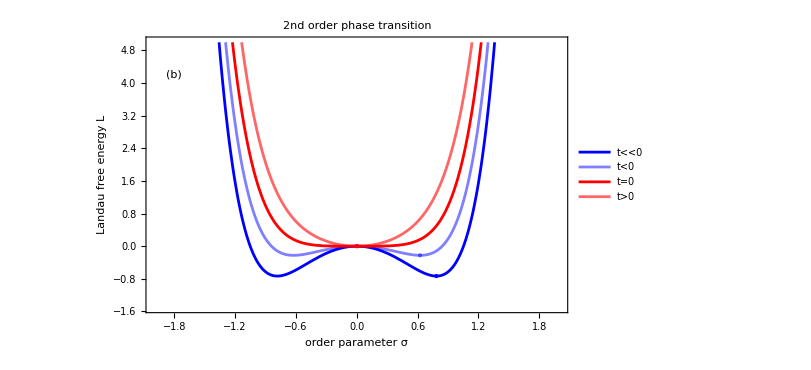

```mathematica
(*All together*)
landau2nd=Show[{Plot[{L[x,-2,0.7,1,0],L[x,-1,0.7,1,0],L[x,0,0.7,1,0],L[x,1.3,0.7,1,0]},
{x,-2,2},
PlotRange->{-1.5,5},
PlotStyle->{
Directive[Opacity[1],Blue,AbsoluteThickness[2]],
Directive[Opacity[0.5],Blue,AbsoluteThickness[2]],
Directive[Opacity[1],Red,AbsoluteThickness[2]],
Directive[Opacity[0.6],Red,AbsoluteThickness[2]]},
Frame->True,
AxesOrigin->{0,0},
FrameLabel->{"order parameter σ","Landau free energy L"},
LabelStyle->{FontSize->16},
PlotLabel->Style["2nd order phase transition",FontSize->20],
ImageSize->{600,400},
PlotLegends->Placed[
LineLegend[
{Text[Style["t<<0",FontSize->13]],
Text[Style["t<0",FontSize->13]],
Text[Style["t=0",FontSize->13]],
Text[Style["t>0",FontSize->13]]}],{Right,Center}]],
ListPlot[{{xmin3[-2,0.7,1,0],L[xmin3[-2,0.7,1,0],-2,0.7,1,0]}},
PlotStyle->{Directive[PointSize[Large],Opacity[1],Blue]}],
ListPlot[{{xmin3[-1,0.7,1,0],L[xmin3[-1,0.7,1,0],-1,0.7,1,0]}},
PlotStyle->{Directive[PointSize[Large],Opacity[0.5],Blue]}],
ListPlot[{{xmin1[0,0.7,1,0],L[xmin1[0,0.7,1,0],0,0.7,1,0]}},
PlotStyle->{Directive[PointSize[Large],Opacity[1],Red]}],ListPlot[{{xmin1[1.3,0.7,1,0],L[xmin1[1.3,0.7,1,0],1.3,0.7,1,0]}},
PlotStyle->{Directive[PointSize[Large],Opacity[0.5],Red]}],
Graphics[{Black,FontSize->18,Text["(b)",{-1.8,4.2}]}]}]
```

```mathematica
Export["landau_energy_2nd.PDF",landau2nd,"PDF"]
```

landau_energy_2nd.PDF

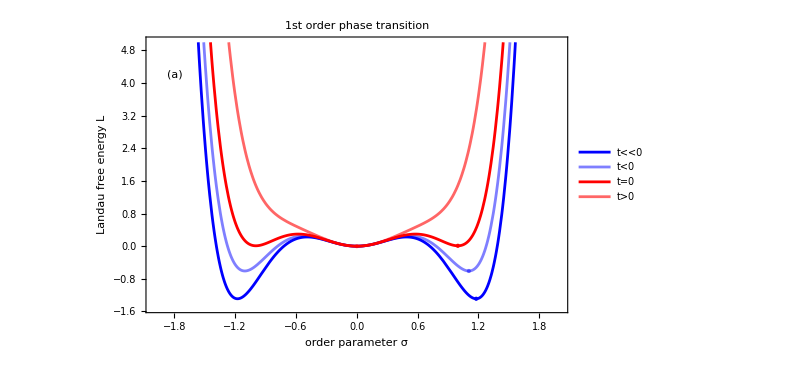

```mathematica
(*All together*)
landau1st=Show[{Plot[{L[x,2,-4.9,2.01,0],L[x,2,-4.5,2.01,0],L[x,2,-4,2.01,0],L[x,2,-2.5,2.01,0]},
{x,-2,2},
PlotRange->{-1.5,5},
PlotStyle->{
Directive[Opacity[1],Blue,AbsoluteThickness[2]],
Directive[Opacity[0.5],Blue,AbsoluteThickness[2]],
Directive[Opacity[1],Red,AbsoluteThickness[2]],
Directive[Opacity[0.6],Red,AbsoluteThickness[2]]},
Frame->True,
AxesOrigin->{0,0},
FrameLabel->{"order parameter σ","Landau free energy L"},
LabelStyle->{FontSize->16},
PlotLabel->Style["1st order phase transition",FontSize->20],
ImageSize->{600,400},
PlotLegends->Placed[
LineLegend[
{Text[Style["t<<0",FontSize->13]],
Text[Style["t<0",FontSize->13]],
Text[Style["t=0",FontSize->13]],
Text[Style["t>0",FontSize->13]]}],{Right,Center}]],
ListPlot[{{xmin5[2,-4.9,2.01,0],L[xmin5[2,-4.9,2.01,0],2,-4.9,2.01,0]}},
PlotStyle->{Directive[PointSize[Large],Opacity[1],Blue]}],
ListPlot[{{xmin5[2,-4.5,2.01,0],L[xmin5[2,-4.5,2.01,0],2,-4.5,2.01,0]}},
PlotStyle->{Directive[PointSize[Large],Opacity[0.5],Blue]}],
ListPlot[{{xmin5[2,-4,2.01,0],L[xmin5[2,-4,2.01,0],2,-4,2.01,0]}},
PlotStyle->{Directive[PointSize[Large],Opacity[1],Red]}],ListPlot[{{xmin1[2,-2.5,2.01,0],L[xmin1[2,-2.5,2.01,0],2,-2.5,2.01,0]}},
PlotStyle->{Directive[PointSize[Large],Opacity[0.5],Red]}],
Graphics[{Black,FontSize->18,Text["(a)",{-1.8,4.2}]}]}]
```

```mathematica
Export["landau_energy_1st.PDF",landau1st,"PDF"]
```

landau_energy_1st.PDF